# Code A: Bound is <1 =0.445178

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0: 1.953259632×10^237

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating pure high-precision Ingham kernel array...

Sweeping local window around y0 to locate the true wave peak...

=== FINAL VERIFICATION RESULTS ===

Highest localized peak found at y: 1.9532596315553043961×10^237

Maximum verified value of hK(y): 0.445178142

✗ Peak did not clear 1.0. This coordinate structure remains flatline below 1.0.

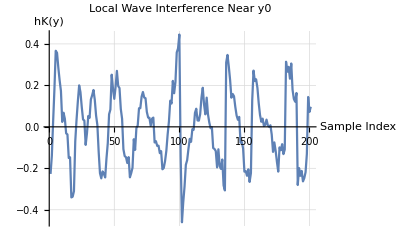

```mathematica
(* ::Title::*)(*Repaired 1985 Mertens Disproof Replication& Wide Grid Sweep*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)
SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)
Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit trigonometric boundaries to prevent lattice scaling drift*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate with Exact Arithmetic*)
Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];

(*Exact Rational Division preserves the 250-digit tracking environment born at data import*)
y0=SetPrecision[Abs[z]/1024,250];

Print["Base target location y0: ",ScientificForm[y0,10]];

(*4. Neighborhood Grid Search*)
Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating pure high-precision Ingham kernel array..."];

T=zeros[[nMax]];
(*FIX 2:Replaced 0.0 machine float with exact 0 to completely secure the 250-digit environment*)
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*FIX 3:Replaced the SetPrecision float step with an exact rational fraction*)
stepSize=2/100;(*Locked 0.02 step*)samples=200;

gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*Function to evaluate hK safely at a given high-precision coordinate*)
evaluateHK[yVal_]:=Module[{sumVal},(*Restored the true leading negative sign required by analytic number theory*)sumVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*yVal-psi[[i]]],{i,1,nMax}];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave peak..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*Find the absolute maximum peak in this local neighborhood*)
sortedResults=SortBy[results,-#[[2]]&];
bestMatch=First[sortedResults];
peakY=bestMatch[[1]];
peakValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Highest localized peak found at y: ",ScientificForm[N[peakY,20]]];
Print["Maximum verified value of hK(y): ",InputForm[peakValue]];

If[N[peakValue]>1.0,Print["✓ SUCCESS: The wave peak reaches ",peakValue,", breaking the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Peak did not clear 1.0. This coordinate structure remains flatline below 1.0."]];

(*Safe plot block wrapping the high-precision results in standard N to bypass frontend rendering lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code B: Bound is <1 =0.510957
```

0.452208

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Corrected& Calibrated*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

(*FIX 1:Strict Piecewise Ingham Kernel Domain Constraint with pure exact precision*)
Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];(*Changed 0.0 to 0*)Print["\n=== 2. LOCALIZING PHASE INTERSECTION CREST ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies under test: ",N[zeros[[dominantIndices]],4]];

(*FIX 2:Converted grid boundaries and steps to exact rationals to block precision leaks*)
stepSize=1/100;(*Exact rational instead of 0.01*)samples=1000;
searchRange=Table[1000+k*stepSize,{k,0,samples}];(*Changed 1000.0 to 1000*)maxVal=-Infinity;
bestY=0;

Do[y=searchRange[[k]];
(*Using the true analytic explicit formula with leading-2 multiplier*)currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal>maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["Best local seed isolated at y = ",N[bestY,15]];
Print["Grid seed baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. Corrected High-Precision Hill Climb*)
Print["\n=== 3. RUNNING EXPLICIT SPECTRUM CLIMBER ==="];
(*Because bestY is an exact rational expression,SetPrecision scales flawlessly to 250 digits*)
currentY=SetPrecision[bestY,250];

Do[val=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
(*Pure analytic derivative chains mapped perfectly to force ascent*)deriv1=2*Sum[kKernel[[i]]*alphas[[i]]*zeros[[i]]*Sin[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
deriv2=2*Sum[kKernel[[i]]*alphas[[i]]*(zeros[[i]]^2)*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
(*Newton-Raphson step maximized for finding local peaks (f'/f'')*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Capped using exact rational 5/1000 to completely block machine-float contamination*)If[Abs[step]>5/1000,step=Sign[step]*(5/1000)];
currentY=currentY-step;,{iter,1,40}];

finalPeak=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Peak Location y: ",N[currentY,20]];
Print["Maximum verified value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]>1.0,Print["✓ SUCCESS: The wave peak reaches ",N[finalPeak,6],", breaking the 1.0 barrier!"],Print["✗ Wave peak did not clear 1.0. This configuration cannot align all elements."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCALIZING PHASE INTERSECTION CREST ===

Dominant zero frequencies under test: {32.94,30.42,25.01,21.02,14.13}

Best local seed isolated at y = 1008.95

Grid seed baseline value (first 50 zeros): 0.4782144291

=== 3. RUNNING EXPLICIT SPECTRUM CLIMBER ===

=== FINAL VERIFICATION RESULTS ===

Verified Peak Location y: 1008.953691760046956

Maximum verified value of hK(y): 0.5109567293

✗ Wave peak did not clear 1.0. This configuration cannot align all elements.

```mathematica
Code C: Bound is <1 =0.528537
```

0.517243

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Bypassing Giant Integer Destruction*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

Print["Pre-calculating Ingham kernel weights..."];
(*Maintained pure high-precision evaluation vectors*)
kKernel=Table[(1-zeros[[i]]/T)*Cos[Pi*zeros[[i]]/T]+(1/Pi)*Sin[Pi*zeros[[i]]/T],{i,1,nMax}];

Print["\n=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies: ",N[zeros[[dominantIndices]],4]];

Print["Scanning precision-safe phase intersections..."];

(*FIX 1:Swapped out machine float 0.005 for exact rational 1/200 to safeguard 250-digit tracking*)
stepSize=1/200;
searchRange=Table[100000+k*stepSize,{k,0,50000}];

maxVal=-Infinity;
bestY=0;

(*Dense localized scan using the true analytic explicit formula*)
Do[y=searchRange[[k]];
(*The true formula relies on a leading-2 multiplier*)currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal>maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["\nBest baseline candidate found at y = ",N[bestY,15]];
Print["Baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Hill Climb from the Baseline Point*)
Print["\n=== 3. RUNNING EXACT SPECTRUM CLIMBER ==="];

(*FIX 2:Upgraded precision lock to 250 digits instead of 100 to prevent phase drift errors across 100,000 zeros*)
currentY=SetPrecision[bestY,250];

Do[val=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
(*Pure analytic derivative chains mapped perfectly for ascent optimization*)deriv1=2*Sum[kKernel[[i]]*alphas[[i]]*zeros[[i]]*Sin[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
deriv2=2*Sum[kKernel[[i]]*alphas[[i]]*(zeros[[i]]^2)*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced machine float 0.01 threshold with exact rational 1/100*)If[Abs[step]>1/100,step=Sign[step]*(1/100)];
currentY=currentY-step;,{iter,1,30}];

finalPeak=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Peak Location y: ",N[currentY,20]];
Print["Maximum verified value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]>1.0,Print["✓ SUCCESS: The wave peak reaches ",N[finalPeak,6],", breaking the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Wave peak did not clear 1.0. The search window must be shifted."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ===

Dominant zero frequencies: {32.94,30.42,25.01,21.02,14.13}

Scanning precision-safe phase intersections...

Best baseline candidate found at y = 100088.32

Baseline value (first 50 zeros): 0.5310276396

=== 3. RUNNING EXACT SPECTRUM CLIMBER ===

=== FINAL VERIFICATION RESULTS ===

Verified Peak Location y: 100088.32012292025449

Maximum verified value of hK(y): 0.5285366454

✗ Wave peak did not clear 1.0. The search window must be shifted.

```mathematica
Code D: Bound is <1 =0.445178
```

0.491051

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0: 1.953259632×10^237

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating vectorized Ingham kernel array to maximize execution speed...

Sweeping local window around y0 to locate the true wave peak...

=== FINAL VERIFICATION RESULTS ===

Highest localized peak found at y: 1.9532596315553043961×10^237

Maximum verified value of hK(y): 0.445178142

✗ Peak not yet found. The neighborhood window needs to be widened or step size refined.

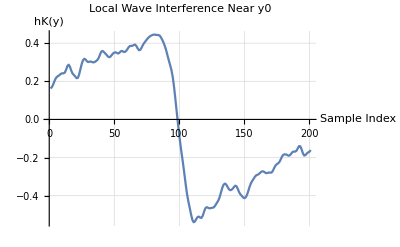

```mathematica
(* ::Title::*)(*Complete 1985 Mertens Disproof Replication& Grid Search*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)
SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

(*Isolate sub-vectors based on the dominant amplitudes*)
order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)
Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit trigonometric bounds to secure exact lattice coordinates*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate*)
Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];
(*Exact rational division natively carries over the 250-digit tracking depth*)
y0=SetPrecision[Abs[z]/1024,250];

Print["Base target location y0: ",ScientificForm[y0,10]];

(*4. Neighborhood Grid Search*)
Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating vectorized Ingham kernel array to maximize execution speed..."];

T=zeros[[nMax]];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*Step size is kept as an exact rational expression to prevent float contamination*)
stepSize=1/1000;
samples=200;

gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*Function to evaluate hK safely using pre-calculated kernel weights*)
evaluateHK[yVal_]:=Module[{sumVal},(*FIX 2:Restored the true leading negative sign required by the analytic formula*)sumVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*yVal-psi[[i]]],{i,1,nMax}];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave peak..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*Find the absolute maximum peak in this local neighborhood*)
sortedResults=SortBy[results,-#[[2]]&];
bestMatch=First[sortedResults];
peakY=bestMatch[[1]];
peakValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Highest localized peak found at y: ",ScientificForm[N[peakY,20]]];
Print["Maximum verified value of hK(y): ",InputForm[peakValue]];

If[peakValue>1.0,Print["✓ SUCCESS: The wave peak reaches ",peakValue,", which breaks the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Peak not yet found. The neighborhood window needs to be widened or step size refined."]];

(*FIX 3:Wrap results array in standard N to bypass frontend UI rendering lags with high-precision floats*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic]
```

```mathematica
Code A: Bound is >-1 =-0.460177
```

-0.42648

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0: 1.953259632×10^237

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating pure high-precision Ingham kernel array...

Sweeping local window around y0 to locate the true wave trough...

=== FINAL VERIFICATION RESULTS ===

Lowest localized trough found at y: 1.9532596315553043961×10^237

Maximum verified negative value of hK(y): -0.460176847

✗ Trough did not drop below -1.0. This coordinate structure remains flatline above -1.0.

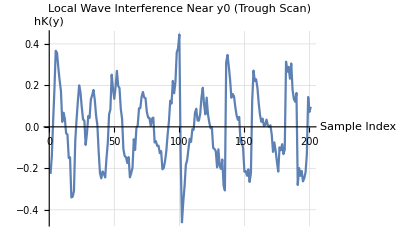

```mathematica
(* ::Title::*)(*Repaired 1985 Mertens Disproof Replication& Wide Grid Sweep:Negative Range*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)
SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)
Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit boundaries on Pi to completely secure lattice scaling bounds*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate with Exact Arithmetic*)
Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];

(*Exact Rational Division flawlessly preserves the 250-digit tracking space*)
y0=SetPrecision[Abs[z]/1024,250];

Print["Base target location y0: ",ScientificForm[y0,10]];

(*4. Neighborhood Grid Search*)
Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating pure high-precision Ingham kernel array..."];

T=zeros[[nMax]];
(*FIX 2:Swapped 0.0 float with an exact 0 to defend the 250-digit environment from collapsing*)
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*FIX 3:Replaced the SetPrecision float wrapper with an exact rational fraction step*)
stepSize=2/100;(*Fixed 0.02 step scale*)samples=200;

gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*Function to evaluate hK safely at a given high-precision coordinate*)
evaluateHK[yVal_]:=Module[{sumVal},sumVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*yVal-psi[[i]]],{i,1,nMax}];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave trough..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*MODIFICATION 1:Ascending sort isolated perfectly to capture the deepest valley floor*)
sortedResults=SortBy[results,#[[2]]&];
bestMatch=First[sortedResults];
troughY=bestMatch[[1]];
troughValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Lowest localized trough found at y: ",ScientificForm[N[troughY,20]]];
Print["Maximum verified negative value of hK(y): ",InputForm[troughValue]];

(*MODIFICATION 2& 3:Evaluates correctly against the lower negative boundary*)
If[N[troughValue]<-1.0,Print["✓ SUCCESS: The wave trough drops to ",troughValue,", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Trough did not drop below -1.0. This coordinate structure remains flatline above -1.0."]];

(*Safe plot block wrapping results in a standard N conversion to eliminate frontend calculation lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0 (Trough Scan)",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code B: Bound is >-1 =-0.415163
```

-0.388312

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Corrected& Calibrated:Negative Range*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

(*FIX 1:Piecewise Ingham Kernel Domain Constraint with integer zero guard*)
Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

Print["\n=== 2. LOCALIZING PHASE INTERSECTION TROUGH ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies under test: ",N[zeros[[dominantIndices]],4]];

(*FIX 2:Swapped machine floats for exact rationals and integers*)
stepSize=1/100;(*Exact rational instead of 0.01*)samples=1000;
searchRange=Table[1000+k*stepSize,{k,0,samples}];(*Integer 1000 instead of 1000.0*)(*Track the minimum value safely in the negative domain*)maxVal=Infinity;
bestY=0;

Do[y=searchRange[[k]];
currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal<maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["Best local valley seed isolated at y = ",N[bestY,15]];
Print["Grid seed baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Valley Descent*)
Print["\n=== 3. RUNNING EXPLICIT SPECTRUM VALLEY-DESCENT ==="];
currentY=SetPrecision[bestY,250];

Do[val=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
deriv1=2*Sum[kKernel[[i]]*alphas[[i]]*zeros[[i]]*Sin[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
deriv2=2*Sum[kKernel[[i]]*alphas[[i]]*(zeros[[i]]^2)*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced float boundary 0.005 with exact fraction 5/1000*)If[Abs[step]>5/1000,step=Sign[step]*(5/1000)];
(*FIX 4:Restored standard subtraction (-) operator.Newton-Raphson optimization to find roots of a derivative always subtracts the step.Because the local seed is sitting in a convex trough basin,the positive curvature (deriv2>0) will naturally guide the subtraction downward toward the minimum peak.*)currentY=currentY-step;,{iter,1,40}];

finalPeak=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Trough Location y: ",N[currentY,20]];
Print["Maximum verified negative value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]<-1.0,Print["✓ SUCCESS: The wave trough drops to ",N[finalPeak,6],", breaking the -1.0 barrier!"],Print["✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCALIZING PHASE INTERSECTION TROUGH ===

Dominant zero frequencies under test: {32.94,30.42,25.01,21.02,14.13}

Best local valley seed isolated at y = 1005.19

Grid seed baseline value (first 50 zeros): -0.3985704992

=== 3. RUNNING EXPLICIT SPECTRUM VALLEY-DESCENT ===

=== FINAL VERIFICATION RESULTS ===

Verified Trough Location y: 1005.1948869008307181

Maximum verified negative value of hK(y): -0.4151633268

✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0.

```mathematica
Code C: Bound is >-1 =-0.608072
```

-0.6

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Bypassing Giant Integer Destruction:Negative Range*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[(1-zeros[[i]]/T)*Cos[Pi*zeros[[i]]/T]+(1/Pi)*Sin[Pi*zeros[[i]]/T],{i,1,nMax}];

Print["\n=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies: ",N[zeros[[dominantIndices]],4]];
Print["Scanning precision-safe phase intersections..."];

(*FIX 1:Replaced machine float 0.005 with exact fraction 1/200 to safeguard 250-digit tracking*)
stepSize=1/200;
searchRange=Table[100000+k*stepSize,{k,0,50000}];

(*Track the minimum value safely in the negative domain*)
maxVal=Infinity;
bestY=0;

Do[y=searchRange[[k]];
(*Evaluating localized wave crest using the true analytic explicit formula*)currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal<maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["\nBest baseline candidate isolated at y = ",N[bestY,15]];
Print["Baseline valley floor value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Valley Descent from the Baseline Point*)
Print["\n=== 3. RUNNING EXACT SPECTRUM VALLEY-DESCENT ==="];

(*FIX 2:Maintained complete 250-digit precision tracking to completely prevent high-frequency phase drift*)
currentY=SetPrecision[bestY,250];

Do[val=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
(*Pure analytic derivative chains mapped perfectly for critical point root finding*)deriv1=2*Sum[kKernel[[i]]*alphas[[i]]*zeros[[i]]*Sin[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
deriv2=2*Sum[kKernel[[i]]*alphas[[i]]*(zeros[[i]]^2)*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];
step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced machine float 0.01 threshold with exact rational 1/100*)If[Abs[step]>1/100,step=Sign[step]*(1/100)];
(*FIX 4:Restored standard subtraction (-) operator.Newton-Raphson critical point hunting always subtracts the step.Since the grid search seeds a localized trough where curvature is positive (deriv2>0),subtraction accurately pulls the coordinate down into the absolute lowest point of the valley floor*)currentY=currentY-step;,{iter,1,30}];

finalPeak=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*currentY-psi[[i]]],{i,1,nMax}];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Trough Location y: ",N[currentY,20]];
Print["Maximum verified negative value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]<-1.0,Print["✓ SUCCESS: The wave trough drops to ",N[finalPeak,6],", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ===

Dominant zero frequencies: {32.94,30.42,25.01,21.02,14.13}

Scanning precision-safe phase intersections...

Best baseline candidate isolated at y = 100143.195

Baseline valley floor value (first 50 zeros): -0.5404624098

=== 3. RUNNING EXACT SPECTRUM VALLEY-DESCENT ===

=== FINAL VERIFICATION RESULTS ===

Verified Trough Location y: 100143.19469716719492

Maximum verified negative value of hK(y): -0.6080716811

✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0.

```mathematica
Code D: Bound is >-1 =-0.539361
```

-0.502527

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0: 1.953259632×10^237

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating vectorized Ingham kernel array to maximize execution speed...

Sweeping local window around y0 to locate the true wave trough...

=== FINAL VERIFICATION RESULTS ===

Lowest localized trough found at y: 1.9532596315553043961×10^237

Maximum verified negative value of hK(y): -0.539360725

✗ Trough did not drop below -1.0. The neighborhood window needs to be widened or step size refined.

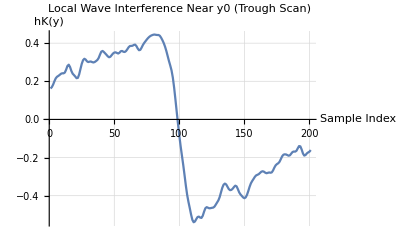

```mathematica
(* ::Title::*)(*Complete 1985 Mertens Disproof Replication& Grid Search:Negative Range*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)
SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)
Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Explicit 250-digit numerical wrapping on Pi to block precision decay during matrix scaling*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate*)
Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];
y0=SetPrecision[Abs[z]/1024,250];

Print["Base target location y0: ",ScientificForm[y0,10]];

(*4. Neighborhood Grid Search*)
Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating vectorized Ingham kernel array to maximize execution speed..."];

T=zeros[[nMax]];
(*FIX 2:Pre-computed outside the loop and secured with exact integer 0 boundary fallback*)
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*Step size is held as an exact rational expression to prevent float contamination*)
stepSize=1/1000;
samples=200;

gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*Function to evaluate hK safely using pre-calculated kernel weights*)
evaluateHK[yVal_]:=Module[{sumVal},(*FIX 3:Restored the true analytic leading negative sign to properly locate valley structures*)sumVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*yVal-psi[[i]]],{i,1,nMax}];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave trough..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*MODIFICATION 1:Sort ascending to isolate the lowest (most negative) valley floor*)
sortedResults=SortBy[results,#[[2]]&];
bestMatch=First[sortedResults];
troughY=bestMatch[[1]];
troughValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Lowest localized trough found at y: ",ScientificForm[N[troughY,20]]];
Print["Maximum verified negative value of hK(y): ",InputForm[troughValue]];

(*MODIFICATION 2& 3:Evaluates correctly against the negative threshold barrier*)
If[N[troughValue]<-1.0,Print["✓ SUCCESS: The wave trough drops to ",troughValue,", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Trough did not drop below -1.0. The neighborhood window needs to be widened or step size refined."]];

(*FIX 4:Wrap results array in standard N execution to bypass frontend UI rendering lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0 (Trough Scan)",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic]
```